```mathematica
(*椭圆沿一条直线滚动时，他的中心点的运动轨迹函数方程是什么？"https://www.zhihu.com/question/627545237"*)
```

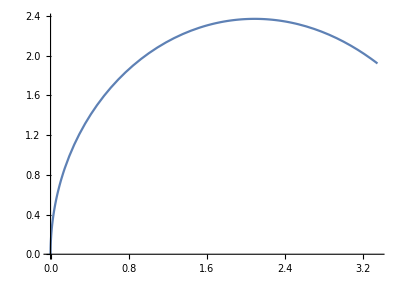

```mathematica
a=4;
b=2;
l[θ_]:=NIntegrate[√(a^2 Sin[t]^2+b^2 Cos[t]^2),{t,0,θ},WorkingPrecision->32]
xd[θ_]:=((-b Sin[θ]+a Cos[θ] Tan[ArcTan[(a Tan[θ])/b]-ArcTan[(l[θ]-b Sin[θ])/(a (1-Cos[θ]))]]+1/2 (l[θ]+Sin[θ])+(a^2 (1-Cos[θ]) (1+Cos[θ]))/(2 (l[θ]-b Sin[θ])))/ ((a (1-Cos[θ]))/(l[θ]-b Sin[θ])+Tan[ArcTan[(a Tan[θ])/b]-ArcTan[(l[θ]-b Sin[θ])/(a (1-Cos[θ]))]]))
yd[θ_]:=-(a*(1-Cos[θ]))/(l[θ]-b Sin[θ])*xd[θ]+1/2 (l[θ]+Sin[θ])+(a*(1-Cos[θ]) a*(1+Cos[θ]))/(2 (l[θ]-b Sin[θ]))
ParametricPlot[{xd[θ]-xd[θ] Cos[ArcTan[(a Tan[θ])/b]]+yd[θ] Sin[ArcTan[(a Tan[θ])/b]],yd[θ]-yd[θ] Cos[ArcTan[(a Tan[θ])/b]]-xd[θ] Sin[ArcTan[(a Tan[θ])/b]]},{θ,-Pi/4,0}]
```

```mathematica
pts=Table[{xd[θ]-xd[θ] Cos[ArcTan[(a Tan[θ])/b]]+yd[θ] Sin[ArcTan[(a Tan[θ])/b]],yd[θ]-yd[θ] Cos[ArcTan[(a Tan[θ])/b]]-xd[θ] Sin[ArcTan[(a Tan[θ])/b]]},{θ,-Pi/4,0,Pi/4/120}]//Most//Rest//Quiet;
```

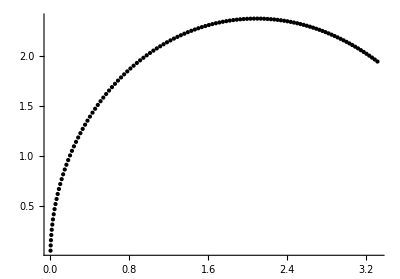

```mathematica
Graphics[{Point[pts]},Axes->True]
```

```mathematica
pts2=Table[{xd[θ] Cos[ArcTan[(a Tan[θ])/b]]+yd[θ] Sin[ArcTan[(a Tan[θ])/b]],yd[θ] Cos[ArcTan[(a Tan[θ])/b]]-xd[θ] Sin[ArcTan[(a Tan[θ])/b]]},{θ,-Pi/4,0,Pi/4/120}]//Most//Rest//Quiet;
```

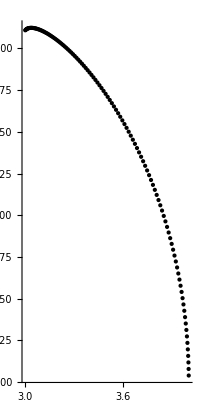

```mathematica
Graphics[{Point[pts2]},Axes->True]
```

```mathematica
L=8 EllipticE[-3];
a=4;
b=2;
r1[t_]={a*Cos[t],b*Sin[t]};
r2[t_]={a,t};
cpt={0,0};
{t1,t2}=Map[Module[{t,s},Function[r,NDSolve[{t'[s]*Norm[r'[t[s]]]==1,t[0]==0},t,{s,0,L}][[1,1,2]]]],{r1,r2}];
{cp1,cp2}={Composition[r1,t1],Composition[r2,t2]};
trans[cp2_,cp1_,s_,cl_]:=cp1[s]//TranslationTransform[cp2[cl]-cp1[cl]]//RotationTransform[{cp1'[cl],cp2'[cl]},cp2[cl]];
trans2[pts_,cp2_,cp1_,cl_]:=pts//TranslationTransform[cp2[cl]-cp1[cl]]//RotationTransform[{cp1'[cl],cp2'[cl]},cp2[cl]];
Manipulate[Show[ParametricPlot[{cp2[s]}//Evaluate,{s,0,L},PlotStyle->{Cyan},PlotRange->{{-4.1,5},{-2.1,22}}],ParametricPlot[{trans[cp2,cp1,s,cl]}//Evaluate,{s,0,L},PlotStyle->{Blue}],Graphics[{PointSize[0.02],Point[{{a,cl},trans2[cpt,cp2,cp1,cl]}]}],Graphics[{PointSize[0.01],Point[pts]}],ImageSize->{200,400}],{{cl,0,"step"},0,L,L/60,Appearance->"Labeled"},SaveDefinitions->True,ControlPlacement->Top]
```